{x→0.593012}

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[380-20 s-15 Sin[3.3458 s]==t,s]

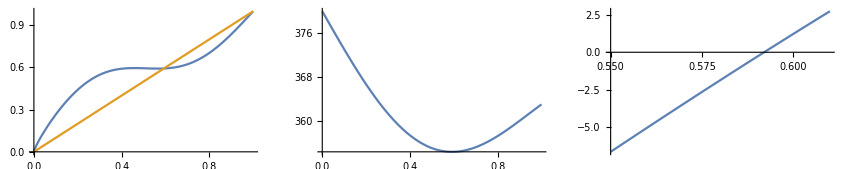

```mathematica
Module[{eqdata,eqtempdata,eqtempdata2},
eqdata[x_]:=x^0.75+0.15*Sin[2π*x];
eqtempdata[x_]:=380-20*x-15*Sin[1.065*π*x];
Print[FindRoot[eqdata[x]==x,{x,0.25,0.75}]];

GraphicsRow@{Plot[{eqdata[x],x},{x,0,1}],Plot[eqtempdata[x],{x,0,1}],Plot[eqtempdata'[x],{x,0.55,0.61}]}
]
```